```mathematica
epsilon = 0.08; d = 0.7; c = 0.8; ff[v_]:=v-v^3/3;
```

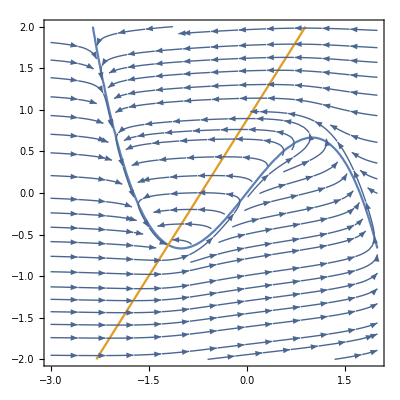

```mathematica
II = 0; (*Part A*)
Show[ContourPlot[{v-v^3/3-w+II==0,epsilon*(v + d- c*w)==0},{v,-3,2},{w,-2,2}],StreamPlot[{v-v^3/3-w+II,epsilon*(v + d- c*w)},{v,-3,2},{w,-2,2}]]
```

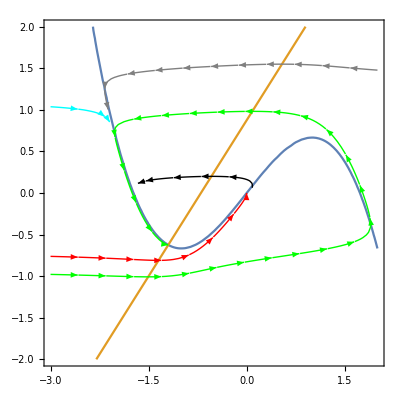

```mathematica
Show[ContourPlot[{v-v^3/3-w+II==0,epsilon*(v + d- c*w)==0},{v,-3,2},{w,-2,2}],StreamPlot[{v-v^3/3-w+II,epsilon*(v + d- c*w)},{v,-3,2},{w,-2,2},StreamPoints->{{  {  {0,0} , Red }  ,    {  {-2,-1} , Green  },{  {-2.5,1} ,Cyan  } ,{  {-1,1.5} , Gray}  ,{  {-0.5,0.2} , Black } }  }] ]
```

```mathematica
points= Join[Table[{v,v-v^3/3+II},{v,-2,2,0.2}],Table[{c*w-d,w},{w,-2,2,0.2}]];
```

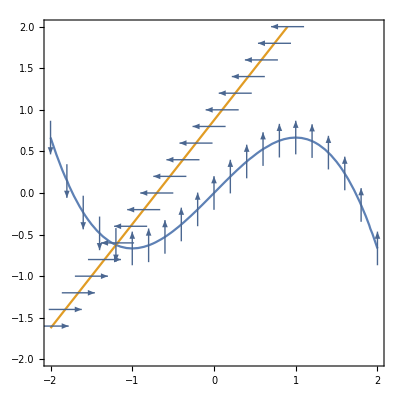

```mathematica
Show[ContourPlot[{v-v^3/3-w+II==0,epsilon*(v + d- c*w)==0},{v,-2,2},{w,-2,2}],VectorPlot[{(v-v^3/3-w+II)/Sqrt[(v-v^3/3-w+II)^2+(epsilon*(v + d- c*w))^2],(epsilon*(v + d- c*w))/Sqrt[(v-v^3/3-w+II)^2+(epsilon*(v + d- c*w))^2]},{v,-2,2},{w,-2,2},VectorPoints->points]]
```

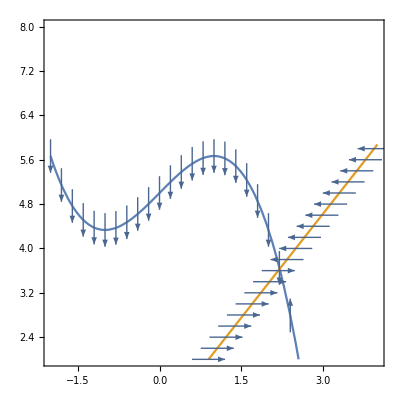

```mathematica
II3 = 5; points2= Join[Table[{v,v-v^3/3+II3},{v,-2,4,0.2}],Table[{c*w-d,w},{w,2,8,0.2}]];
Show[ContourPlot[{v-v^3/3-w+II3==0,epsilon*(v + d- c*w)==0},{v,-2,4},{w,2,8}],VectorPlot[{(v-v^3/3-w+II3)/Sqrt[(v-v^3/3-w+II3)^2+(epsilon*(v + d- c*w))^2],(epsilon*(v + d- c*w))/Sqrt[(v-v^3/3-w+II3)^2+(epsilon*(v + d- c*w))^2]},{v,-2,4},{w,2,8},VectorPoints->points2]]
```

5

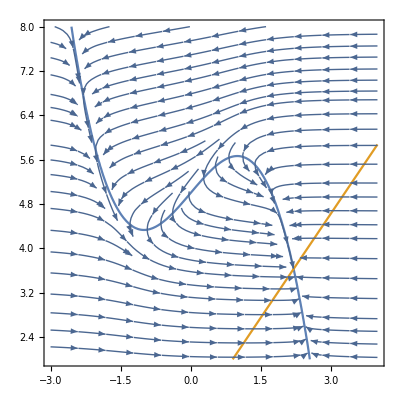

```mathematica
II2 = 5  (*Part B*)
Show[ContourPlot[{v-v^3/3-w+II2==0,epsilon*(v + d- c*w)==0},{v,-3,4},{w,2,8}],StreamPlot[{v-v^3/3-w+II2,epsilon*(v + d- c*w)},{v,-3,4},{w,2,8}]]
```

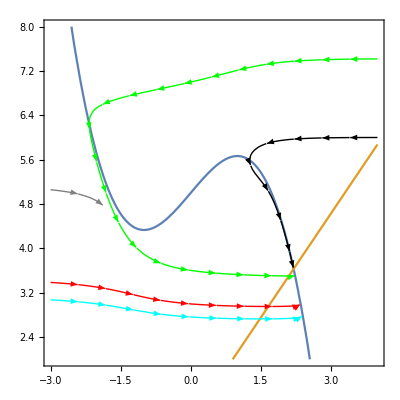

```mathematica
II2=5;Show[ContourPlot[{v-v^3/3-w+II2==0,epsilon*(v + d- c*w)==0},{v,-3,4},{w,2,8}],StreamPlot[{v-v^3/3-w+II2,epsilon*(v + d- c*w)},{v,-3,4},{w,2,8},StreamPoints->{{  {  {0,3} , Red }  ,    {  {0,7} , Green  },{  {-2,3} ,Cyan  } ,{  {-2.5,5} , Gray}  ,{  {3.5,6} , Black } }  }] ]
```

```mathematica
Manipulate[Show[ContourPlot[{v-v^3/3-w+IIv==0,epsilon*(v + d- c*w)==0},{v,-3,6},{w,-3,6}],StreamPlot[{v-v^3/3-w+IIv,epsilon*(v + d- c*w)},{v,-3,6},{w,-3,6}]],{IIv,0,10}]
```